```mathematica
ClearAll["Global`*"];
NotebookFind[EvaluationNotebook[],"Output",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookFind[EvaluationNotebook[],"Print",All,CellStyle];FrontEndExecute[FrontEndToken["Clear"]];
NotebookDelete@Cells@MessagesNotebook[];
On[Assert];
```

```mathematica
Get[NotebookDirectory[]<>"VecG.m"]
Get[NotebookDirectory[]<>"Functions.m"];

G=SymmetricGroup[3];(*Left fusion category*)
H=PermutationGroup[{Cycles[{{1,2}}]}];(*Subgp of G labelling the module*)

(*G=DihedralGroup[4];(*Left fusion category*)
H=PermutationGroup[{Cycles[{{1,3},{2,4}}]}];(*Subgp of G labelling the module*)*)
```

```mathematica
computeMoritaDual[G,H];(*Computes all data as discussed in paper*)
```

Computing module action

Computing irreps

Computing intertwiners

Verifying isometric

Isometric: ✓

```mathematica
fusionTable["C"](*Fusion rules for left fusion category (input data)*)
fusionTable["L"](*Fusion rules for M as left module category (input data)*)
fusionTable["R"](*Fusion rules for M as right module category (computed)*)
fusionTable["D"](*Fusion rules for right fusion category (computed)*)
dim[#]&/@obsD
```

| 1 | σ_2\[PermutationProduct]σ_1 | σ_1 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2
1 | 1 | σ_2\[PermutationProduct]σ_1 | σ_1 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2
σ_2\[PermutationProduct]σ_1 | σ_2\[PermutationProduct]σ_1 | 1 | σ_2 | σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2^2
σ_1 | σ_1 | σ_2^2 | 1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_2
σ_2 | σ_2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_2^2 | 1 | σ_1
σ_2^2 | σ_2^2 | σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | 1 | σ_2 | σ_2\[PermutationProduct]σ_1
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2 | σ_2^2 | σ_2\[PermutationProduct]σ_1 | σ_1 | 1

| H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
1 | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_1 | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H
σ_2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H
σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2 | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H

| ℼ_0 | ℼ_1 | ℼ_2
H | H | H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]H | H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H
σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | σ_2\[PermutationProduct]σ_1\[PermutationProduct]σ_2^2\[PermutationProduct]H | H⊕σ_2\[PermutationProduct]σ_1\[PermutationProduct]H

| ℼ_0 | ℼ_1 | ℼ_2
ℼ_0 | ℼ_0 | ℼ_1 | ℼ_2
ℼ_1 | ℼ_1 | ℼ_0 | ℼ_2
ℼ_2 | ℼ_2 | ℼ_2 | ℼ_0⊕ℼ_1⊕ℼ_2

{1,1,2}

```mathematica
Fs[0](*F-symbols for left fusion category (input data)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Fs[1](*F-symbols for M as a left module category (input data)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Fs[2](*F-symbols for M as a bimodule category (computed using Eq.13)*)
```

{1,1,1,1,1,1,1,1,1,1,1,1,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,4]0.6834995288741615,Root0.879+0.477 ⅈRoot[4457-4864 #1^2+4457 #1^4&,4]0.8791070795688043,Root-0.917-0.400 ⅈRoot[2691157457-3661465136 #1^2+2691157457 #1^4&,1]-0.9165906985468051,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,Root0.683-0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,3]0.6834995288741615,Root0.879-0.477 ⅈRoot[4457-4864 #1^2+4457 #1^4&,3]0.8791070795688043,Root-0.917+0.400 ⅈRoot[2691157457-3661465136 #1^2+2691157457 #1^4&,2]-0.9165906985468051,1,-1,Root-0.611-0.792 ⅈRoot[6814477+3458904 #1^2+6814477 #1^4&,1]-0.6108228617253534,Root-0.611+0.792 ⅈRoot[6814477+3458904 #1^2+6814477 #1^4&,2]-0.6108228617253534,1,-1,Root-0.953-0.302 ⅈRoot[21257-34770 #1^2+21257 #1^4&,1]-0.9533751198314878,Root-0.953+0.302 ⅈRoot[21257-34770 #1^2+21257 #1^4&,2]-0.9533751198314878,Root0.954+0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,4]0.9541782860950396,Root-0.222-0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,1]-0.22213813026054383,Root-0.197-0.980 ⅈRoot[416056493+767407050 #1^2+416056493 #1^4&,1]-0.19718138567247342,Root-0.474+0.880 ⅈRoot[9241873+10168704 #1^2+9241873 #1^4&,2]-0.4742662604662846,Root0.954-0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,3]0.9541782860950396,Root-0.222+0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,2]-0.22213813026054383,Root-0.197+0.980 ⅈRoot[416056493+767407050 #1^2+416056493 #1^4&,2]-0.19718138567247342,Root-0.474-0.880 ⅈRoot[9241873+10168704 #1^2+9241873 #1^4&,1]-0.4742662604662846,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root-0.683-0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,1]-0.6834995288741615,Root0.753+0.658 ⅈRoot[126601-34080 #1^2+126601 #1^4&,4]0.7531919055718171,Root-0.982-0.189 ⅈRoot[94742449-175933680 #1^2+94742449 #1^4&,1]-0.9819582260406458,Root0.954+0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,4]0.9541782860950396,Root0.222+0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,4]0.22213813026054383,Root-0.656+0.755 ⅈRoot[325361+91040 #1^2+325361 #1^4&,2]-0.655779637137526,Root-0.407-0.913 ⅈRoot[11818076749+15791508598 #1^2+11818076749 #1^4&,1]-0.40736456237988267,Root-0.883+0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,2]-0.8829709657859577,Root0.560+0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,4]0.5598819712765326,Root0.294+0.956 ⅈRoot[93349+154440 #1^2+93349 #1^4&,4]0.2939232141574226,Root0.787+0.617 ⅈRoot[1551761-738078 #1^2+1551761 #1^4&,4]0.7867081681917932,Root-0.883-0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,1]-0.8829709657859577,Root0.560-0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,3]0.5598819712765326,Root0.294-0.956 ⅈRoot[93349+154440 #1^2+93349 #1^4&,3]0.2939232141574226,Root0.787-0.617 ⅈRoot[1551761-738078 #1^2+1551761 #1^4&,3]0.7867081681917932,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,Root-0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,2]-0.6834995288741615,Root-0.982+0.189 ⅈRoot[94742449-175933680 #1^2+94742449 #1^4&,2]-0.9819582260406458,Root0.753-0.658 ⅈRoot[126601-34080 #1^2+126601 #1^4&,3]0.7531919055718171,Root0.954-0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,3]0.9541782860950396,Root0.222-0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,3]0.22213813026054383,Root-0.407+0.913 ⅈRoot[11818076749+15791508598 #1^2+11818076749 #1^4&,2]-0.40736456237988267,Root-0.656-0.755 ⅈRoot[325361+91040 #1^2+325361 #1^4&,1]-0.655779637137526,Root-0.883-0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,1]-0.8829709657859577,Root-0.560+0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,2]-0.5598819712765326,Root-0.936+0.351 ⅈRoot[73-110 #1^2+73 #1^4&,2]-0.9363291775690445,Root8.24 × 10^-3+1.00 ⅈRoot[1984319693+3968100664 #1^2+1984319693 #1^4&,4]0.00823846951057322,1,-1,Root0.976+0.219 ⅈRoot[564260657-1019986590 #1^2+564260657 #1^4&,4]0.9756602176841843,Root0.976-0.219 ⅈRoot[564260657-1019986590 #1^2+564260657 #1^4&,3]0.9756602176841843,Root-0.883+0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,2]-0.8829709657859577,Root-0.560-0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,1]-0.5598819712765326,Root8.24 × 10^-3-1.00 ⅈRoot[1984319693+3968100664 #1^2+1984319693 #1^4&,3]0.00823846951057322,Root-0.936-0.351 ⅈRoot[73-110 #1^2+73 #1^4&,1]-0.9363291775690445}

```mathematica
Fs[3](*F-symbols for M as a right module category (computed using intertwiners)*)
```

{1,1,-1,-1,1,1,1,-1,1,Root0.954+0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,4]0.9541782860950396,1,Root-0.222-0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,1]-0.22213813026054383,Root0.379+0.597 ⅈRoot[6127627088633015113798841854261+27619764469422351933945696743680 #1^2+78259853768329051920757034378088 #1^4+110479057877689407735782786974720 #1^6+98042033418128241820781469668176 #1^8&,8]0.3792156178259887,Root-0.373-0.601 ⅈRoot[175567283627746000052792039125+817856089202643134095600627360 #1^2+2303532267151412422687071312744 #1^4+3271424356810572536382402509440 #1^6+2809076538043936000844672626000 #1^8&,1]-0.37271828222931574,Root0.894+0.447 ⅈRoot[4176033186631777-5012794801612896 #1^2+4176033186631777 #1^4&,4]0.8944792280414328,Root-0.634+0.313 ⅈRoot[6127627088633015113798841854261-27992593755329737204801827303680 #1^2+80848500701726108198821409162088 #1^4-111970375021318948819207309214720 #1^6+98042033418128241820781469668176 #1^8&,2]-0.634246285527653,Root-0.638+0.306 ⅈRoot[208760147000887039301774125-986057058363325574334803360 #1^2+2830205663825601403495046184 #1^4-3944228233453302297339213440 #1^6+3340162352014192628828386000 #1^8&,2]-0.6376006332706419,-1,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,4]0.9829826272238078,Root0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,4]0.9829826272238078,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root-0.119-0.993 ⅈRoot[135033121126445+262447902554934 #1^2+135033121126445 #1^4&,1]-0.11876268790050473,Root0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,4]0.6834995288741615,Root-0.683-0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,1]-0.6834995288741615,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,Root0.954+0.299 ⅈRoot[83842769-137655138 #1^2+83842769 #1^4&,4]0.9541782860950396,Root0.683-0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,3]0.6834995288741615,Root0.222+0.975 ⅈRoot[12962410745+23366282766 #1^2+12962410745 #1^4&,4]0.22213813026054383,Root-0.482-0.517 ⅈRoot[420127295216226720392253067325664554200525+1648634664617568068378821353685662143596800 #1^2+3785003563673874591010180228897908296871464 #1^4+6594538658470272273515285414742648574387200 #1^6+6722036723459627526276049077210632867208400 #1^8&,1]-0.48239754441359123,Root-0.693-0.139 ⅈRoot[90539816593581507230250784944062894125-100751057427525209566543517700654380640 #1^2-138084950616869609319938318790391525336 #1^4-403004229710100838266174070802617522560 #1^6+1448637065497304115684012559105006306000 #1^8&,1]-0.693380463327925,Root0.991+0.137 ⅈRoot[41191027961-79278228978 #1^2+41191027961 #1^4&,4]0.9905362165653419,Root0.549+0.446 ⅈRoot[35884003516788077546689859734967484787068135042779567725+112594440108279199111016880485961915199130419696300140800 #1^2+170828888614860322937617367624023908084937798472704545576 #1^4+450377760433116796444067521943847660796521678785200563200 #1^6+574144056268609240747037755759479756593090160684473083600 #1^8&,8]0.5487917985045883,Root-0.706-0.0422 ⅈRoot[7733206421118867038778979754421980331193881093842125-17943518243096327370133948764363495058371752752659040 #1^2+11151829752006915576695623214206437974528711161615656 #1^4-71774072972385309480535795057453980233487011010636160 #1^6+123731302737901872620463676070751685299102097501474000 #1^8&,1]-0.7058482528667046,Root-0.541+0.841 ⅈRoot[81736167957925935973+67784559380838010104 #1^2+81736167957925935973 #1^4&,2]-0.5409923195791119,Root-0.883-0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,1]-0.8829709657859577,Root-0.883-0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,1]-0.8829709657859577,Root0.883+0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,4]0.8829709657859577,Root0.883+0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,4]0.8829709657859577,Root-0.883-0.469 ⅈRoot[8005-8954 #1^2+8005 #1^4&,1]-0.8829709657859577,Root0.765+0.644 ⅈRoot[104327035037605-35528369215034 #1^2+104327035037605 #1^4&,4]0.7649424910321416,Root0.560-0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,3]0.5598819712765326,Root-0.560+0.829 ⅈRoot[570805+425894 #1^2+570805 #1^4&,2]-0.5598819712765326,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,1,Root-0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,2]-0.6834995288741615,-1,Root0.413-0.574 ⅈRoot[392658497030280824317607630992091236525-1072225482028644126567129248307582060800 #1^2+1151706681051693722784067698796323586344 #1^4-4288901928114576506268516993230328243200 #1^6+6282535952484493189081722095873459784400 #1^8&,5]0.41326830934462383,Root0.610+0.357 ⅈRoot[2720715449171406934197491794367594125+5322653291518093932002227622331060320 #1^2+892214906532003960559354760008404264 #1^4+21290613166072375728008910489324241280 #1^6+43531447186742510947159868709881506000 #1^8&,8]0.6102932131127473,Root0.651-0.759 ⅈRoot[10574439643997+3206253495544 #1^2+10574439643997 #1^4&,3]0.6513048659200074,Root0.657+0.261 ⅈRoot[33537832577813213625984353533930744153844366785211725+22669459079723263558058698431488314394940655410796800 #1^2-81227687804116137849935456351562263922083778036184024 #1^4+90677836318893054232234793725953257579762621643187200 #1^6+536605321245011418015749656542891906461509868563387600 #1^8&,8]0.6570760054252847,Root0.198-0.679 ⅈRoot[195433545509903813830742824543364680062746386119527125+59968945486678164421062666113722449476868212137080480 #1^2-458102709619710086562214655105086456165467138102090904 #1^4+239875781946712657684250664454889797907472848548321920 #1^6+3126936728158461021291885192693834881003942177912434000 #1^8&,5]0.19791145120604636,Root0.108+0.994 ⅈRoot[8844112871701+17276549519002 #1^2+8844112871701 #1^4&,4]0.10787498764371097}

```mathematica
Fs[4](*F-symbols for right fusion category (computed as maps between intertwiners)*)
```

{1,1,-1,1,1,-1,1,1,-1,-1,1,1,1,-1,1,1,-1,1,1,Root-1.00+0.0108 ⅈRoot[13753947557096877953249836201686625-55000100765706937831658790326840860 #1^2+82492310755270674400353406894706694 #1^4-55000100765706937831658790326840860 #1^6+13753947557096877953249836201686625 #1^8&,2]-0.9999411459709623,Root-1.00-0.0108 ⅈRoot[13753947557096877953249836201686625-55000100765706937831658790326840860 #1^2+82492310755270674400353406894706694 #1^4-55000100765706937831658790326840860 #1^6+13753947557096877953249836201686625 #1^8&,1]-0.9999411459709623,-1,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,4]0.9829826272238078,Root0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,4]0.9829826272238078,Root0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,4]0.9829826272238078,Root-0.983-0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,1]-0.9829826272238078,Root-0.119-0.993 ⅈRoot[135033121126445+262447902554934 #1^2+135033121126445 #1^4&,1]-0.11876268790050473,Root0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,4]0.6834995288741615,Root0.683+0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,4]0.6834995288741615,Root-0.683-0.730 ⅈRoot[22709+2982 #1^2+22709 #1^4&,1]-0.6834995288741615,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,Root-0.983+0.184 ⅈRoot[261845-488346 #1^2+261845 #1^4&,2]-0.9829826272238078,1,Root-0.691+0.722 ⅈRoot[7092892613738032149708920192675842487841625+1921470329434317512109529958659071477727140 #1^2+14299935239793476919773044431281301272766614 #1^4+1921470329434317512109529958659071477727140 #1^6+7092892613738032149708920192675842487841625 #1^8&,2]-0.6913786676299647,Root-0.676+0.737 ⅈRoot[7092892613738032149708920192675842487841625+1803039584241807142225943939486035667877540 #1^2+14284379306939143211357013152286614201214614 #1^4+1803039584241807142225943939486035667877540 #1^6+7092892613738032149708920192675842487841625 #1^8&,4]-0.6755399367170245,-1,Root0.491-0.0918 ⅈRoot[261845-1953384 #1^2+4189520 #1^4&,3]0.4914913136119039,Root0.346-0.361 ⅈRoot[7092892613738032149708920192675842487841625+7685881317737270048438119834636285910908560 #1^2+228798963836695630716368710900500820364265824 #1^4+122974101083796320775009917354180574574536960 #1^6+1815780509116936230325483569325015676887456000 #1^8&,7]0.345689333814982,Root-0.650+0.278 ⅈRoot[78629898121512935352733777182867362920912850149+70935348135540310946762968205123684854764869120 #1^2-168965894066494006075009099339028091005918284008 #1^4+283741392542161243787051872820494739419059476480 #1^6+1258078369944206965643740434925877806734605602384 #1^8&,2]-0.6503092684497425,Root0.490-0.0972 ⅈRoot[37720368437094429641920465254383617773546625-563089144542968439330763936923678890589000432 #1^2+3308322292680640360950946663200695638318045280 #1^4-9009426312687495029292222990778862249424006912 #1^6+9656414319896173988331639105122206150027936000 #1^8&,5]0.49046589857201894,Root0.342-0.365 ⅈRoot[22709+11928 #1^2+363344 #1^4&,3]0.34174976443708077,Root0.647-0.285 ⅈRoot[2678816588065856639026879386928293658892125+2472521835866523594863311393533402399247040 #1^2-4826353871751292283585571332487797594079144 #1^4+9890087343466094379453245574133609596988160 #1^6+42861065409053706224430070190852698542274000 #1^8&,7]0.6472585589587114,Root-0.690-0.153 ⅈRoot[5391086295411007023091980212986951591515099318870079049725-4193561497922874355074813330990606458963830312375877260800 #1^2-12445864695384753107279856769940825666479990431971479519144 #1^4-16774245991691497420299253323962425835855321249503509043200 #1^6+86257380726576112369471683407791225464241589101921264795600 #1^8&,1]-0.6902493700967908,Root0.650-0.278 ⅈRoot[1381462181106482609881254823385009681471332783787125-6475826997523138169580132863993567856827697617184960 #1^2+18396241243050784633097886574411190446692090296726936 #1^4-25903307990092552678320531455974271427310790468739840 #1^6+22103394897703721758100077174160154903541324540594000 #1^8&,7]0.6502208637649051,1,-1,0}

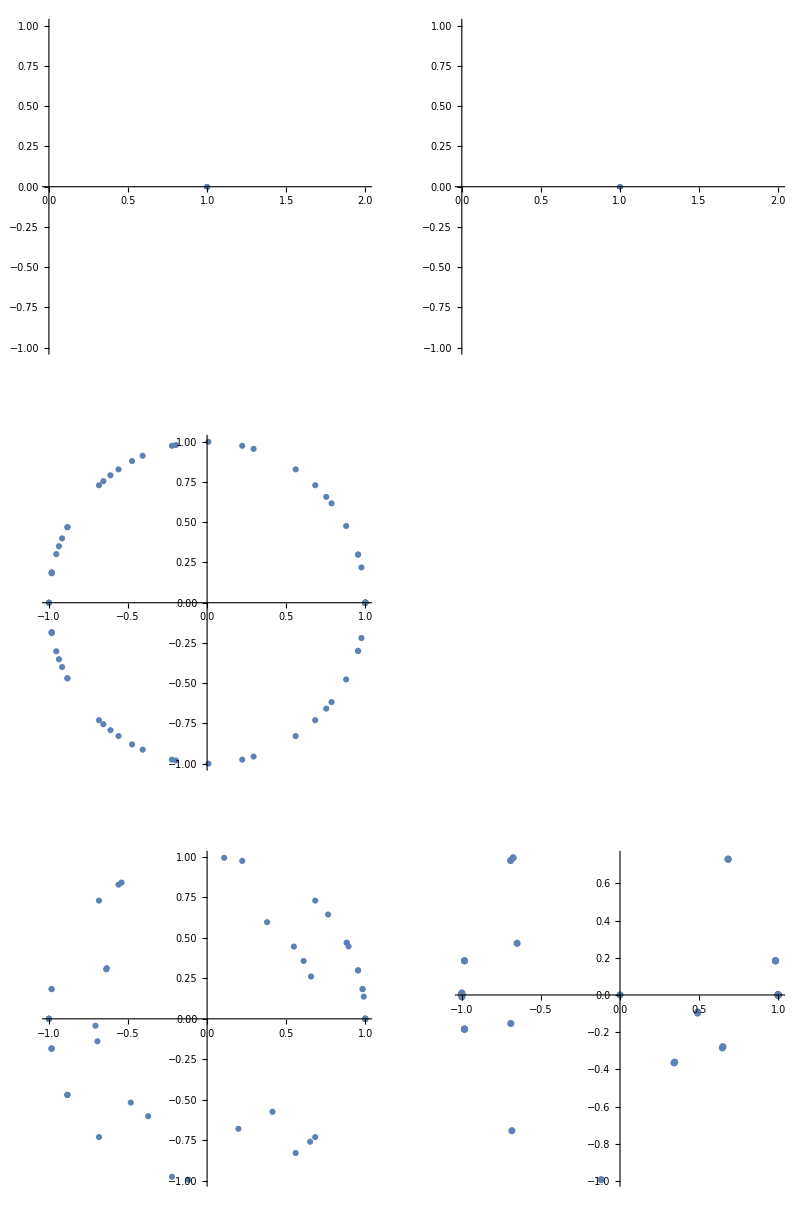

```mathematica
plt[n_]:=ListPlot[{Re[#],Im[#]}&/@Fs[n],AspectRatio->1]
GraphicsGrid[{{plt[0],plt[1]},{plt[2]},{plt[3],plt[4]}}]
```

```mathematica
verifyData[](*Check data is unitary and obeys pentagons*)
```

Pentagons: ✓

Unitary: ✓

```mathematica
verifyInvertibility[](*Verify invertiblility formula holds*)
```

Invertibility criteria: ✓

```mathematica
schurOrthogQ[](*Verify matrix element orthogonalityholds*)
```

Schur orthogonality: ✓